# Games on finite graphs

Like Nowak’s games on finite populations but with a graph structure added.

```mathematica
Get["/home/leo/thesis/code/graphs.m"]
```

## Code

### Functions

```mathematica
(* i is always the amount of type 𝒜 individuals *)
f[i_]:=1.-w+w(a(i-1)+b(n-i))/(n-1);
g[i_]:=1.-w+w(c i+d(n-i-1))/(n-1);
η[i_]:=i f[i]+(n-i)g[i];
rf[i_]:=f[i]/η[i];
rg[i_]:=g[i]/η[i];
(*relFitness[type_,i_]:=If[type===𝒜,rf@i,rg@i];*)
relFitness[𝒜,i_]:=rf@i;
relFitness[ℬ,i_]:=rg@i;
```

```mathematica
(* Transition probabilities for Subscript[i, t] *)
SubPlus[p][i_]:=(i f[i])/η[i](n-i)/n;SubPlus[p][_?((#>n)||(#<0)&)]=0;
SubMinus[p][i_]:=((n-i)g[i])/η[i] i/n;SubMinus[p][_?(#>n||(#<0)&)]=0;
Subscript[p, 0][i_]:=1-SubPlus[p][i]-SubMinus[p][i];Subscript[p, 0][_?(#>n||(#<0)&)]=0;

(* P[t, m] is the probability that Subscript[i, t]=m *)
Subscript[i, 0]=25;
P[0,Subscript[i, 0]]:=1;
P[0,_]:=0;
P[_?(#<0&),_]:=0;
P[_,_?(#>n&)]:=0;
P[_,_?(#<0&)]:=0;
P[t_,k_]:=P[t,k]=P[t-1,k+1]SubMinus[p][k+1]+P[t-1,k]Subscript[p, 0][k]+P[t-1,k-1]SubPlus[p][k-1];
```

```mathematica
(* Pei[t, m, k] is the probability that Subscript[e, t]=m and Subscript[i, t]=k *)
Subscript[e, 0]=0;
Pei[0,Subscript[e, 0],k_]:=P[0,k];
Pei[0,_,_]:=0;
Pei[_?(#<0&),_,_]:=0;
Pei[_,_,_?((#>n)||(#<0)&)]:=0;
Pei[_,_?((#<0)||(#>n(n-1)/2)&),_]:=0;
Pei[_,m_,k_]:=0/;m>k(k-1)/2;
Pei[t_,m_,k_]:=Pei[t,m,k]=
(1-Subscript[ec, t]/((n-i)i))(i f[i])/η[i](n-i)/n Pei[t-1,m-1,k-1]+
Pei[t-1,m-1,k]+
Pei[t-1,m-1,k+1]+
Pei[t-1,m,k-1]+
Pei[t-1,m,k]+
Pei[t-1,m,k+1]+
Pei[t-1,m+1,k-1]+
Pei[t-1,m+1,k]+
Pei[t-1,m+1,k+1];
```

```mathematica
(* "Transition" probabilities for Subscript[e, t] *)
(*q_+[i_,e_]:=(f[i](n i-2 e))/(η[i]n);
q_-[i_,e_]:=0;
Subscript[q, 0][i_,e_]:=(2e f[i]+n g[i](n-i))/(η[i]n);*)

(* Pe[t, m] is the probability that Subscript[e, t]=m *)
Pe[0,0]:=1;
Pe[0,_Except[0]]:=0;
Pe[_,_?(#>n(n-1)/2&)]:=0;
Pe[_?(#<0&),_]:=0;
Pe[t_,m_]:=Pe[t,m]=Sum[Pei[t,m,k],{k,0,n}];
```

### Steps & Processes

```mathematica
step[graph_,types_]:=
Module[{nodes=VertexList@graph,edges=EdgeList@graph,newtypes,newedges,h,k},
h=RandomChoice[relFitness[#,Count[types,𝒜]]&/@types->nodes];
k=RandomChoice[nodes];
(* node h "reproduces" *)
newtypes=types;
newtypes⟦k⟧=types⟦h⟧;
(* and, according to the strategy (type), add or delete the edge *)
newedges=Switch[types⟦h⟧,
𝒜,getSimpleGraphEdges@Append[edges,h<->k],
ℬ,Complement[edges,{h<->k}]];
{Graph[nodes,newedges],newtypes}]
```

```mathematica
Options[converge]:={max->1000}
converge[graph_,types_,OptionsPattern[]]:=NestWhile[step@@#&,{graph,types},0<Count[#⟦2⟧,𝒜]<n&,1,OptionValue[max]]
```

## Test

```mathematica
n=50;
(* playing Prisonner's dilemma *)
a=2;b=0;c=3;d=1;
```

### Strong selection

```mathematica
w=1;
graph=Graph[Range@n,{}];
types=RandomChoice[{𝒜,ℬ},n];
```

```mathematica
Row@Table[converge[graph,types]⟦1⟧,{5}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
w=0.8;
graph=Graph[Range@n,{}];
types=RandomChoice[{𝒜,ℬ},n];
```

```mathematica
Row@Table[converge[graph,types]⟦1⟧,{5}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

### Medium selection

```mathematica
w=0.6;
graph=Graph[Range@n,{}];
types=RandomChoice[{𝒜,ℬ},n];
```

```mathematica
Row@Table[converge[graph,types]⟦1⟧,{5}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
w=0.4;
graph=Graph[Range@n,{}];
types=RandomChoice[{𝒜,ℬ},n];
```

```mathematica
Row@Table[converge[graph,types]⟦1⟧,{5}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

### Weak selection

```mathematica
w=0.35;
graph=Graph[Range@n,{}];
types=RandomChoice[{𝒜,ℬ},n];
```

```mathematica
Row@Table[converge[graph,types]⟦1⟧,{5}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
w=0.2;
graph=Graph[Range@n,{}];
types=RandomChoice[{𝒜,ℬ},n];
```

```mathematica
Row@Table[converge[graph,types]⟦1⟧,{5}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

### Big graph

```mathematica
n=150;
(* playing Prisonner's dilemma *)
a=-1;b=-3;c=0;d=-2;
```

```mathematica
w=0.8;
graph=Graph[Range@n,{}];
types=RandomChoice[{𝒜,ℬ},n];
```

```mathematica
res=converge[graph,types,max->10000];//AbsoluteTiming
```

{9.27926,Null}

```mathematica
res
```

{-Graphics-,{ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ,ℬ}}

## Transition probabilities

```mathematica
n=50;
(* playing Prisonner's dilemma *)
(*a=-1;b=-3;c=0;d=-2;*)
w=1;
```

Explore the bahavior of the transition probabilities p_+,p_-,p_0 of the Markov chain {i_t} and the probabilities associated with the variables {e_t} q_+,q_-,q_0.

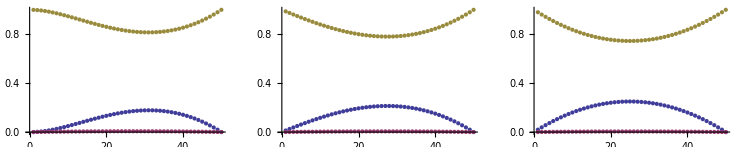

```mathematica
GraphicsRow[{
Block[{w=1},ListPlot[{SubPlus[p]/@Range@n,SubMinus[p]/@Range@n,Subscript[p, 0]/@Range@n}]],
Block[{w=0.35},ListPlot[{SubPlus[p]/@Range@n,SubMinus[p]/@Range@n,Subscript[p, 0]/@Range@n}]],
Block[{w=0},ListPlot[{SubPlus[p]/@Range@n,SubMinus[p]/@Range@n,Subscript[p, 0]/@Range@n}]]}]
```

```mathematica
ListPlot3D[Block[{w=0},Table[SubPlus[q][i,e],{i,Range@n},{e,Range[n(n-1)/2]}]]]
```

```mathematica
ListPointPlot3D[Table[{i,e,Subscript[q, 0][i,e]},{i,Range@n},{e,Range[2i]}]]
```

```mathematica
Sum[m P[0,m],{m,0,n}]
```

25

```mathematica
Tally@Table[Sum[P[t,m],{m,0,n}],{t,0,500}]
```

{{1,1},{1.,9},{1.,62},{1.,75},{1.,35},{1.,42},{1.,106},{1.,118},{1.,53}}

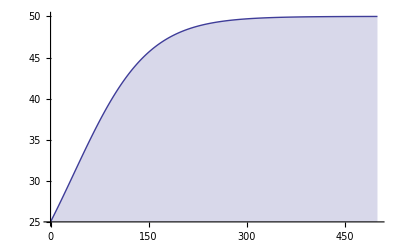

```mathematica
DiscretePlot[Sum[m P[t,m],{m,0,n}],{t,0,500}]
```

```mathematica
probs=Table[Pei[t,m,k],{t,100},{k,0,n},{m,0,k(k-1)/2}];//AbsoluteTiming
```

{189.90759,Null}

```mathematica
Length@Flatten@probs
```

2087600

```mathematica
(*Save["/home/leo/thesis/code/dump/Pei.m",Pei];*)
```

```mathematica
ps=Table[Pe[t,m],{t,0,500},{m,0,n(n-1)/2}];//AbsoluteTiming
```

{914.82769,Null}

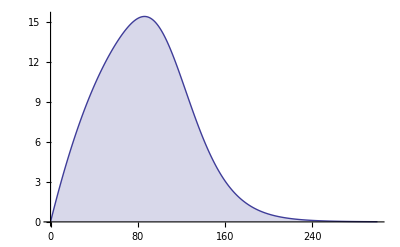

```mathematica
DiscretePlot[Sum[m Pe[t,m],{m,0,n(n-1)/2}],{t,0,300}]
```

## Play

```mathematica
w=1;
n=9;
graph=Graph[Range@n,{}];
types=RandomChoice[{𝒜,ℬ},n];
```

```mathematica
HighlightGraph[graph,Pick[Range@n,types,𝒜],VertexLabels->"Name"]
```

-Graphics-

```mathematica
{graph,types}=step[graph,types];
HighlightGraph[graph,Pick[Range@n,types,𝒜],VertexLabels->"Name"]
```

-Graphics-

```mathematica
{graph,types}=step[graph,types];
HighlightGraph[graph,Pick[Range@n,types,𝒜],VertexLabels->"Name"]
```

-Graphics-

```mathematica
{graph,types}=step[graph,types];
HighlightGraph[graph,Pick[Range@n,types,𝒜],VertexLabels->"Name"]
```

-Graphics-

```mathematica
{graph,types}=step[graph,types];
HighlightGraph[graph,Pick[Range@n,types,𝒜],VertexLabels->"Name"]
```

-Graphics-

```mathematica
{graph,types}=step[graph,types];
HighlightGraph[graph,Pick[Range@n,types,𝒜],VertexLabels->"Name"]
```

-Graphics-

```mathematica
{graph,types}=step[graph,types];
HighlightGraph[graph,Pick[Range@n,types,𝒜],VertexLabels->"Name"]
```

-Graphics-

```mathematica
{graph,types}=step[graph,types];
HighlightGraph[graph,Pick[Range@n,types,𝒜],VertexLabels->"Name"]
```

-Graphics-

```mathematica
?*ombi*
```